```mathematica
$Assumptions={ω >0,T>0,Ω>0};
```

```mathematica
Tval=1;
Ωval=20 Pi;

yRamseyFinite[t_,T_,Ω_]:=Piecewise[{{Sin[Ω t],0<t<π/(2 Ω)},{1,π/(2 Ω)<t<π/(2 Ω)+T},{Sin[Ω (π/( Ω)+T-t)],π/(2 Ω)+T<t<π/Ω+T}},0]

yRamseyFinite[t_,T_,Ω_]:=Module[{τ=Pi/(2 Ω)},Piecewise[{{Sin[Ω t],0<t<τ},{1,τ<=t<=τ+T},{Cos[Ω (t-τ-T)],τ+T<t<2 τ+T}},0]]
```

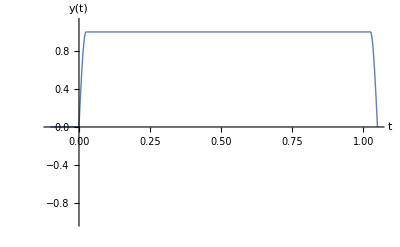

```mathematica
Plot[yRamseyFinite[t,Tval,Ωval],{t,-0.1,Tval+Pi/Ωval},AxesLabel->{"t","y(t)"},PlotRange->{-1,1.1},PlotStyle->Thick,Exclusions->None]
```

```mathematica
HRamseyFinite[ω_, T_, Ω_] := 
  
    Integrate[
      yRamseyFinite[t1, T, Ω] Exp[I ω t1],
      {t1, 0, π/Ω + T}
    ]// FullSimplify
```

```mathematica
HRamseyFinite[ω,T,Ω]//FullSimplify
```

(Ω (-2 (1+ⅇ^(2 ⅈ f π (T+π/Ω))) f π+ⅈ ⅇ^((ⅈ f π^2)/Ω) (-1+ⅇ^(2 ⅈ f π T)) Ω))/(8 f^3 π^3-2 f π Ω^2)

```mathematica
-(Ω (ω+ⅇ^((ⅈ ω (π+T Ω))/Ω) ω+2 ⅇ^((ⅈ ω (π+T Ω))/(2 Ω)) Ω Sin[(T ω)/2]))/(ω^3-ω Ω^2)(-Ω (ω+ⅇ^((-ⅈ ω (π+T Ω))/Ω) ω+2 ⅇ^((-ⅈ ω (π+T Ω))/(2 Ω)) Ω Sin[(T ω)/2]))/(ω^3-ω Ω^2)
```

```mathematica
(Ω^2 (ω+ⅇ^(-(ⅈ ω (π+T Ω))/Ω) ω+2 ⅇ^(-(ⅈ ω (π+T Ω))/(2 Ω)) Ω Sin[(T ω)/2]) (ω+ⅇ^((ⅈ ω (π+T Ω))/Ω) ω+2 ⅇ^((ⅈ ω (π+T Ω))/(2 Ω)) Ω Sin[(T ω)/2]))/((ω^3-ω Ω^2)^2)//FullSimplify
```

(4 Ω^2 (ω Cos[(ω (π+T Ω))/(2 Ω)]+Ω Sin[(T ω)/2])^2)/((ω^3-ω Ω^2)^2)

```mathematica
ω = 2 π f
```

2 f π

```mathematica
HFramsey = (4 Ω^2 (ω Cos[(ω (π+T Ω))/(2 Ω)]+Ω Sin[(T ω)/2])^2)/(T^2(ω^3-ω Ω^2)^2)
```

(4 Ω^2 (2 f π Cos[(f π (π+T Ω))/Ω]+Ω Sin[f π T])^2)/(T^2 (8 f^3 π^3-2 f π Ω^2)^2)

```mathematica
LowPass = (Ω^2/(Ω^2-(2π f)^2))^2
```

Ω^4/((-4 f^2 π^2+Ω^2)^2)

```mathematica
HFramsey/LowPass//FullSimplify
```

```mathematica
HFramsey = (2 f/Ω π Cos[(f π (π+T Ω))/Ω]+Sin[f π T])^2/(f^2 π^2 T^2)(Ω^2/(Ω^2-(2π f)^2))^2
```

```mathematica
Sphi = A/((2π f)^2+B^2)
```

A/(B^2+4 f^2 π^2)

```mathematica
(2 f/Ω π Cos[(f π (π+T Ω))/Ω]+Sin[f π T])^2/(f^2 π^2 T^2)
```